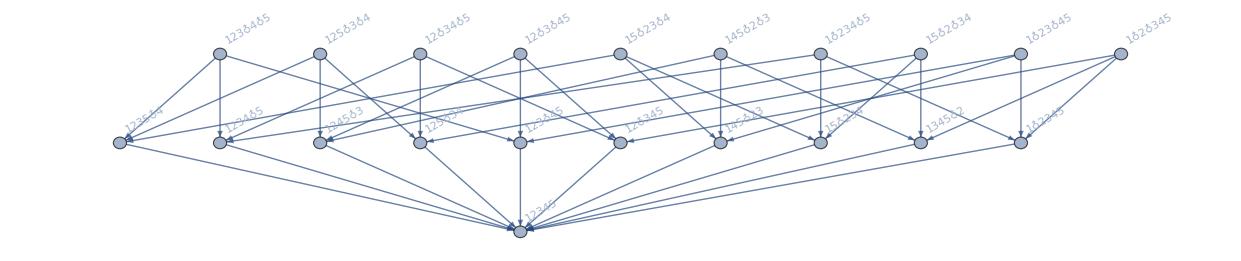

```mathematica
Graph[FormulaGraphReverse2[Map[allGraphs5[#,"colofour"]&,Select[allGraphs5AtomKeys,allGraphs5[#,"atleast"]!=0&]]],  GraphHighlightStyle->"Thick"]
```

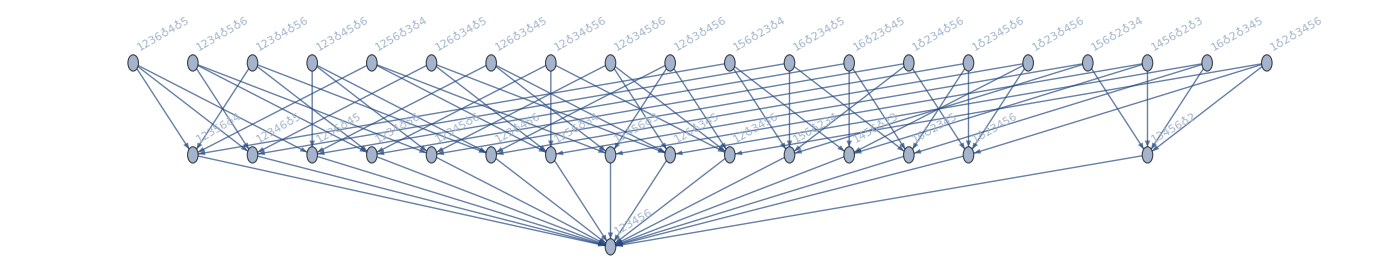

```mathematica
Graph[FormulaGraphReverse2[Map[allGraphs6[#,"colofour"]&,Select[allGraphs6AtomKeys,allGraphs6[#,"comp"]===Greater&]]],  GraphHighlightStyle->"Thick"]
```

```mathematica
With[{g=Graph[FormulaGraphReverse2[Map[allGraphs6[#,"colofour"]&,Select[allGraphs6AtomKeys,allGraphs6[#,"comp"]===Greater&]]],  GraphHighlightStyle->"Thick"]},
Table[VertexInDegree[g,v],{v,VertexList[g]}]]//Tally//Sort
```

{{0,20},{4,15},{15,1}}

```mathematica
With[{g=Graph[FormulaGraphReverse2[Map[allGraphs6[#,"colofour"]&,Select[allGraphs6AtomKeys,allGraphs6[#,"comp"]===Greater&]]],  GraphHighlightStyle->"Thick"]},
Table[VertexOutDegree[g,v],{v,VertexList[g]}]]//Tally//Sort
```

{{0,1},{1,15},{3,20}}

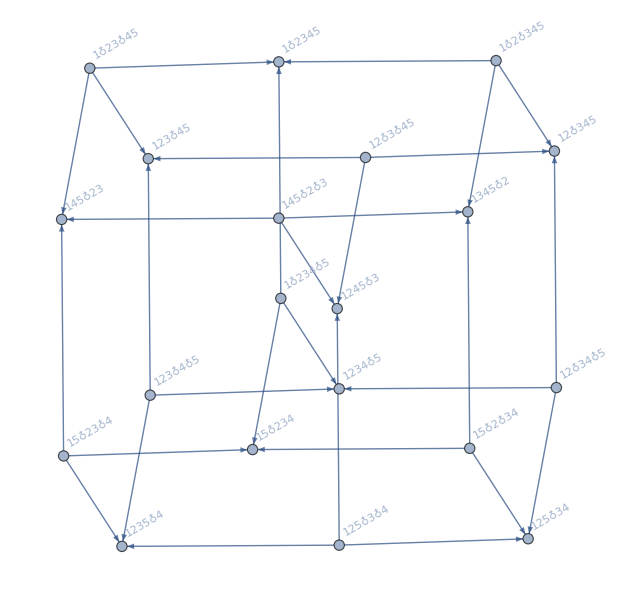

```mathematica
Graph[VertexDelete[Graph[FormulaGraphReverse2[Map[allGraphs5[#,"colofour"]&,Select[allGraphs5AtomKeys,allGraphs5[#,"atleast"]!=0&]]],  GraphHighlightStyle->"Thick"],v12345],GraphLayout->"SpectralEmbedding"]
```